# ReadableForm

Display an expression in a format intended to maximize readability

## Definition

```mathematica
Get["H:\\Documents\\ResourceFunctions\\ReadableForm\\ReadableForm.wl"];
```

## Documentation

### Usage

ReadableForm[expr]

displays a version of expr similar to InputForm[expr] that is formatted to maximize readability.

### Details & Options

ReadableForm has the following options:

CachePersistence | Automatic | specifies how internal caching should be handled
CharacterEncoding | "Unicode" | which character encoding to use
"DynamicAlignment" | False | whether to use context-sensitive alignment across lines
"FormatHeads" | Automatic | a set of heads {h_1,h_2,…} such that h_i[…] should be formatted in StandardForm
"IndentSize" | 4 | how many spaces to use for indenting
"InitialIndent" | 0 | how much additional indentation to apply to each line
PageWidth | 80 | the target character count for each line
PerformanceGoal | "Quality" | aspects of performance to try to optimize
"PrefixForm" | True | whether to use prefix form (f@x) when appropriate
"RealAccuracy" | Automatic | number of digits to the right of the decimal point to display for real numbers
"RelativeWidth" | False | whether to count indentation in page width

Possible settings for CachePersistence include:

None | improves memory usage at the cost of speed
Full | improves speed at the cost of memory usage
Automatic | uses a balanced mix

The "DynamicAlignment" option is considered experimental and is currently only applied for a small set of expression types.

Specifying "InitialIndent"→n will add an additional n×s spaces to the beginning of each line, where s is the value of "IndentSize".

The value for PageWidth specifies a desired target width and is not a hard limit.

The value for "RealAccuracy" can be one of the following:

Automatic | real numbers are displayed using normal InputForm behavior
n | a nonnegative integer specifying a maximum number of digits to display after decimal points

With the setting "RealAccuracy"→n, real numbers will always display with at least one digit to the right of the decimal point. If there are no digits available, a zero will be used.

With the setting "RelativeWidth"→True, the leading whitespace is not counted when determining the width of a line.

## Examples

### Basic Examples

View the code underlying a formatted expression:

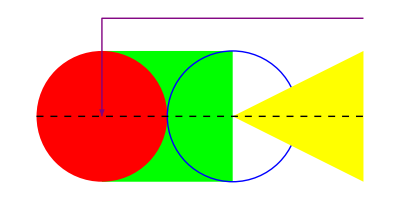
```mathematica
-Graphics-//ReadableForm
```

Graphics @ {
    RGBColor[ 0, 1, 0 ],
    Thickness @ Large,
    Rectangle[ { 0, -1 }, { 2, 1 } ],
    { RGBColor[ 1, 0, 0 ], Disk @ { 0, 0 } },
    { RGBColor[ 0, 0, 1 ], Circle @ { 2, 0 } },
    { RGBColor[ 1, 1, 0 ], Polygon @ { { 2, 0 }, { 4, 1 }, { 4, -1 } } },
    {
        RGBColor[ 0.5, 0, 0.5 ],
        Arrowheads @ Large,
        Arrow @ { { 4, 3 / 2 }, { 0, 3 / 2 }, { 0, 0 } },
        { GrayLevel[ 0 ], Dashing @ { Small, Small }, Line @ { { -1, 0 }, { 4, 0 } } }
    }
}

Visually inspect properties of formatted objects:

```mathematica
ResourceObject[…]//ReadableForm
```

ResourceObject[
    <|
        "Name" -> "LeNet Trained on MNIST Data",
        "UUID" -> "050b1a0a-f43a-4c28-b7e0-72607a918467",
        "ResourceType" -> "NeuralNet",
        "Version" -> "1.16.0",
        "Description" -> "Identify the handwritten digit in an image",
        "RepositoryLocation" ->
            URL[ "https://www.wolframcloud.com/objects/resourcesystem/api/1.0" ],
        "WolframLanguageVersionRequired" -> "11.1",
        "ContentElements" ->
            {
                "ConstructionNotebook",
                "ConstructionNotebookExpression",
                "EvaluationNet",
                "UninitializedEvaluationNet",
                "EvaluationExample"
            }
    |>,
    ResourceSystemBase -> "https://www.wolframcloud.com/objects/resourcesystem/api/1.0"
]

### Scope

Input-style syntax highlighting is used:

```mathematica
ReadableForm[Hold[f[x_]:=Table[i+1,{i,x}]]]
```

Hold[ f[ x_ ] := Table[ i + 1, { i, x } ] ]

Use Unevaluated to prevent the expression from evaluating:

```mathematica
ReadableForm[Unevaluated[Echo[∫_0^1 Log[1/2 (1+√(1+4 x))]/x ⅆx]]]
```

Echo @ Integrate[ Log[(1/2)*(1 + Sqrt[1 + 4*x])]/x, { x, 0, 1 } ]

### Generalizations and Extensions

ToString will preserve the whitespace:

```mathematica
if=ReadableForm[TestResultObject[…]]
```

TestResultObject @ <|
    "TestClass" -> None,
    "TestIndex" -> 1,
    "TestID" -> None,
    "Outcome" -> "MessagesFailure",
    "Input" -> HoldForm[ 1/0 ],
    "ExpectedOutput" -> HoldForm @ DirectedInfinity[ ],
    "ActualOutput" -> HoldForm @ DirectedInfinity[ ],
    "ExpectedMessages" -> { },
    "ActualMessages" -> { HoldForm @ Message[ Power::infy, HoldForm[ 0^(-1) ] ] },
    "AbsoluteTimeUsed" -> Quantity[ 0., "Seconds" ],
    "CPUTimeUsed" -> Quantity[ 0., "Seconds" ],
    "MemoryUsed" -> Quantity[ 1136, "Bytes" ]
|>

```mathematica
ToString[if]
```

TestResultObject @ <|
    "TestClass" -> None,
    "TestIndex" -> 1,
    "TestID" -> None,
    "Outcome" -> "MessagesFailure",
    "Input" -> HoldForm[ 1/0 ],
    "ExpectedOutput" -> HoldForm @ DirectedInfinity[ ],
    "ActualOutput" -> HoldForm @ DirectedInfinity[ ],
    "ExpectedMessages" -> { },
    "ActualMessages" -> { HoldForm @ Message[ Power::infy, HoldForm[ 0^(-1) ] ] },
    "AbsoluteTimeUsed" -> Quantity[ 0., "Seconds" ],
    "CPUTimeUsed" -> Quantity[ 0., "Seconds" ],
    "MemoryUsed" -> Quantity[ 1136, "Bytes" ]
|>

CopyToClipboard will also preserve much of the formatting:

```mathematica
CopyToClipboard[if];
Paste[]
```

```mathematica
TestResultObject @ <|
    "TestClass" -> None,
    "TestIndex" -> 1,
    "TestID" -> None,
    "Outcome" -> "MessagesFailure",
    "Input" -> HoldForm[ 1/0 ],
    "ExpectedOutput" -> HoldForm @ DirectedInfinity[ ],
    "ActualOutput" -> HoldForm @ DirectedInfinity[ ],
    "ExpectedMessages" -> { },
    "ActualMessages" -> { HoldForm @ Message[ Power::infy, HoldForm[ 0^(-1) ] ] },
    "AbsoluteTimeUsed" -> Quantity[ 0., "Seconds" ],
    "CPUTimeUsed" -> Quantity[ 0., "Seconds" ],
    "MemoryUsed" -> Quantity[ 1136, "Bytes" ]
|>
```

### Options

#### CachePersistence

With CachePersistence→None, ReadableForm will not use any caching, which reduces overall memory usage but is the slowest method:

```mathematica
First[RepeatedTiming[ToString[ReadableForm[,CachePersistence->None]]]]
```

0.0192805

With the default behavior of CachePersistence→Automatic, ReadableForm will remember some values between evaluations to gain a modest performance boost:

```mathematica
First[RepeatedTiming[ToString[ReadableForm[,CachePersistence->Automatic]]]]
```

0.0112235

Using CachePersistence→Full will give the fastest performance, but the extra memory used is not released for the remainder of the kernel session:

```mathematica
First[RepeatedTiming[ToString[ReadableForm[,CachePersistence->Full]]]]
```

0.000142261

#### DynamicAlignment

ReadableForm can adjust indentation of certain parts of code in order to obtain alignment across lines when using a monospace font. Here is a helper function to display monospaced results:

```mathematica
showMonospace[expr_]:=Style[ToString[expr],PrivateFontOptions->{"OperatorSubstitution"->False},FontFamily->"Source Code Pro"];
```

```mathematica
showMonospace[expr=]
```

Hold[myFunction[] := Module[{result, anotherResult, test}, result = If[thisThing[], thenDoThatThing[], If[thisThing[], thenDoThatThing[], otherwiseDoSomethingElse[]]]; anotherResult = If[thisThing[], thenDoThatThing[], result = If[thisThing[], thenDoThatThing[], otherwiseDoSomethingElse[]]]; otherFunction[result, anotherResult, test]]]

By default, ReadableForm will only indent one step at a time:

```mathematica
ReadableForm[expr]//showMonospace
```

Hold[
    myFunction[ ] := 
        Module[ { result, anotherResult, test },
            
            result = 
                If[ thisThing[ ],
                    thenDoThatThing[ ],
                    If[ thisThing[ ],
                        thenDoThatThing[ ],
                        otherwiseDoSomethingElse[ ]
                    ]
                ];

            
            anotherResult = 
                If[ thisThing[ ],
                    thenDoThatThing[ ],
                    result = 
                        If[ thisThing[ ],
                            thenDoThatThing[ ],
                            otherwiseDoSomethingElse[ ]
                        ]
                ];

            otherFunction[ result, anotherResult, test ]
        ]
]

Use the setting "DynamicAlignment"→True to perform additional alignment heuristics:

```mathematica
ReadableForm[expr,"DynamicAlignment"->True]//showMonospace
```

Hold[
    myFunction[ ] := 
        Module[ { result, anotherResult, test },
            
            result = If[ thisThing[ ],
                         thenDoThatThing[ ],
                         If[ thisThing[ ],
                             thenDoThatThing[ ],
                             otherwiseDoSomethingElse[ ]
                         ]
                     ];

            
            anotherResult = If[ thisThing[ ],
                                thenDoThatThing[ ],
                                result = If[ thisThing[ ],
                                             thenDoThatThing[ ],
                                             otherwiseDoSomethingElse[ ]
                                         ]
                            ];

            otherFunction[ result, anotherResult, test ]
        ]
]

#### FormatHeads

By default, some expressions are formatted in StandardForm in order to enhance readability:

```mathematica
data=<|"Image"->RandomImage[1,{5,5}],"Time"->Now,"Graphics"->-Graphics-|>;
ReadableForm[data]
```

<|
    "Image" -> -Graphics-,
    "Time" -> "Sat 17 Apr 2021 23:02:21""GMT"-4,
    "Graphics" ->
        Graphics @ {
            RGBColor[ 0, 1, 0 ],
            Thickness @ Large,
            Rectangle[ { 0, -1 }, { 2, 1 } ],
            { RGBColor[ 1, 0, 0 ], Disk @ { 0, 0 } },
            { RGBColor[ 0, 0, 1 ], Circle @ { 2, 0 } },
            { RGBColor[ 1, 1, 0 ], Polygon @ { { 2, 0 }, { 4, 1 }, { 4, -1 } } },
            {
                RGBColor[ 0.5, 0, 0.5 ],
                Arrowheads @ Large,
                Arrow @ { { 4, 3 / 2 }, { 0, 3 / 2 }, { 0, 0 } },
                {
                    GrayLevel[ 0 ],
                    Dashing @ { Small, Small },
                    Line @ { { -1, 0 }, { 4, 0 } }
                }
            }
        }
|>

Use "FormatHeads" to control which expressions are formatted in StandardForm:

```mathematica
ReadableForm[data,"FormatHeads"->{Image,Graphics}]
```

<|
    "Image" -> -Graphics-,
    "Time" ->
        DateObject[
            { 2021, 4, 17, 23, 2, 21.00042 },
            "Instant",
            "Gregorian",
            -4.0
        ],
    "Graphics" -> -Graphics-
|>

Use Automatic to include the defaults:

```mathematica
ReadableForm[data,"FormatHeads"->{Automatic,Graphics}]
```

<|
    "Image" -> -Graphics-,
    "Time" -> "Sat 17 Apr 2021 23:02:21""GMT"-4,
    "Graphics" -> -Graphics-
|>

#### IndentSize

Change the size of indentation in the output:

```mathematica
ReadableForm[SystemInformation["Small"],"IndentSize"->1,"FormatHeads"->None]
```

{
 "Kernel" ->
  {
   "SystemID" -> "Windows-x86-64",
   "ReleaseID" -> "12.3.0.0 (7281235, 202104036916)",
   "CreationDate" ->
    DateObject[ { 2021, 4, 3, 5, 24, 17 }, "Instant", "Gregorian", -4.0 ]
  },
 "FrontEnd" ->
  {
   "OperatingSystem" -> "Windows",
   "ReleaseID" -> "12.3.0.0 (7281235, 202104033193)",
   "CreationDate" ->
    DateObject[ { 2021, 4, 3, 7, 45, 53 }, "Instant", "Gregorian", -4.0 ]
  }
}

#### InitialIndent

Specify an amount of additional indentation to apply to every line:

```mathematica
ReadableForm[<|"Test1"-><|"Name"->"First","Data"->Range[10]|>,"Test2"-><|"Name"->"Second","Data"->{}|>|>,"InitialIndent"->8]
```

<|
                                    "Test1" -> <|
                                        "Name" -> "First",
                                        "Data" ->
                                            { 1, 2, 3, 4, 5, 6, 7, 8, 9, 10 }
                                    |>,
                                    "Test2" -> <| "Name" -> "Second", "Data" -> { } |>
                                |>

#### PageWidth

Set a desired page width to control line breaks:

```mathematica
ReadableForm[SystemInformation["Small"],"PageWidth"->60,"FormatHeads"->None]
```

{
    "Kernel" ->
        {
            "SystemID" -> "Windows-x86-64",
            "ReleaseID" -> "12.3.0.0 (7281235, 202104036916)",
            "CreationDate" ->
                DateObject[
                    { 2021, 4, 3, 5, 24, 17 },
                    "Instant",
                    "Gregorian",
                    -4.0
                ]
        },
    "FrontEnd" ->
        {
            "OperatingSystem" -> "Windows",
            "ReleaseID" -> "12.3.0.0 (7281235, 202104033193)",
            "CreationDate" ->
                DateObject[
                    { 2021, 4, 3, 7, 45, 53 },
                    "Instant",
                    "Gregorian",
                    -4.0
                ]
        }
}

#### PerformanceGoal

By default, ReadableForm will traverse expressions as deep as possible to apply formatting:

```mathematica
RepeatedTiming[ToString[ReadableForm[Unevaluated[],CachePersistence->None]]]
```

{0.00610362,PositionLargest[ list_List ] /; AllTrue[ list, NumericQ ] := 
    First @ FirstPosition[ list, Max @ list ];

PositionLargest[ list_List, n: _Integer | HoldPattern[ UpTo ][ _Integer ] ] /; AllTrue[ list, NumericQ ] := 
    Take[
        Flatten[
            Function[ Position[ list, # ] ] /@ DeleteDuplicates @ TakeLargest[ list, n ]
        ],
        n
    ]}

With PerformanceGoal→"Speed", ReadableForm traverses only deep enough to format lines and uses InputForm to handle the rest:

```mathematica
RepeatedTiming[ToString[ReadableForm[Unevaluated[],CachePersistence->None,PerformanceGoal->"Speed"]]]
```

{0.00292512,PositionLargest[list_List] /; AllTrue[list, NumericQ] := 
    First @ FirstPosition[list, Max[list]];

PositionLargest[list_List, n:_Integer | HoldPattern[UpTo][_Integer]] /; AllTrue[list, NumericQ] := 
    Take[
        Flatten[
            Function[ Position[list, #1] ] /@ DeleteDuplicates @ TakeLargest[list, n]
        ],
        n
    ]}

#### PrefixForm

By default, ReadableForm will use Prefix formatting (f@expr) for some expressions:

```mathematica
ReadableForm[Unevaluated[]]
```

PositionLargest[ list_List ] /; AllTrue[ list, NumericQ ] := 
    First @ FirstPosition[ list, Max @ list ];

PositionLargest[ list_List, n: _Integer | HoldPattern[ UpTo ][ _Integer ] ] /; AllTrue[ list, NumericQ ] := 
    Take[
        Flatten[
            Function[ Position[ list, # ] ] /@ DeleteDuplicates @ TakeLargest[ list, n ]
        ],
        n
    ]

Disable Prefix formatting:

```mathematica
ReadableForm[Unevaluated[],"PrefixForm"->False]
```

PositionLargest[ list_List ] /; AllTrue[ list, NumericQ ] := 
    First[ FirstPosition[ list, Max[ list ] ] ];

PositionLargest[ list_List, n: _Integer | HoldPattern[ UpTo ][ _Integer ] ] /; AllTrue[ list, NumericQ ] := 
    Take[
        Flatten[
            Function[ Position[ list, # ] ] /@ DeleteDuplicates[ TakeLargest[ list, n ] ]
        ],
        n
    ]

#### RealAccuracy

By default, ReadableForm displays real numbers with all available digits:

```mathematica
ReadableForm[RandomReal[1000,5]]
```

{
    914.6871142694797,
    786.1670916044989,
    405.90349695938676,
    820.3904435664194,
    741.146627269143
}

Specify a maximum number of digits to display:

```mathematica
ReadableForm[RandomReal[1000,5],"RealAccuracy"->3]
```

{ 746.55, 474.694, 476.713, 455.685, 858.99 }

#### RelativeWidth

By default, measuring "PageWidth" per line includes the leading whitespace:

```mathematica
expr=<|
"Test1"-><|"Name"->"First","Data"->Range[10]|>,
"Test2"-><|"Name"->"Second","Data"->{}|>
|>;
ReadableForm[expr,"IndentSize"->12,"PageWidth"->45]
```

<|
            "Test1" -> <|
                        "Name" -> "First",
                        "Data" ->
                                    {
                                                1,
                                                2,
                                                3,
                                                4,
                                                5,
                                                6,
                                                7,
                                                8,
                                                9,
                                                10
                                    }
            |>,
            "Test2" -> <|
                        "Name" -> "Second",
                        "Data" -> { }
            |>
|>

Set "RelativeWidth" to True if you don't want to count the leading whitespace:

```mathematica
ReadableForm[expr,"IndentSize"->12,"PageWidth"->45,"RelativeWidth"->True]
```

<|
            "Test1" -> <|
                        "Name" -> "First",
                        "Data" -> { 1, 2, 3, 4, 5, 6, 7, 8, 9, 10 }
            |>,
            "Test2" -> <| "Name" -> "Second", "Data" -> { } |>
|>

### Applications

Copy expressions to the clipboard that will be formatted nicely when pasting into email, etc.:

```mathematica
SystemInformation["Small"]//ReadableForm//CopyToClipboard;
Paste[]
```

```mathematica
{
    "Kernel" ->
        {
            "SystemID" -> "Windows-x86-64",
            "ReleaseID" -> "12.3.0.0 (7281235, 202104036916)",
            "CreationDate" ->
                DateObject[
                    { 2021, 4, 3, 5, 24, 17 },
                    "Instant",
                    "Gregorian",
                    -4.0
                ]
        },
    "FrontEnd" ->
        {
            "OperatingSystem" -> "Windows",
            "ReleaseID" -> "12.3.0.0 (7281235, 202104033193)",
            "CreationDate" ->
                DateObject[
                    { 2021, 4, 3, 7, 45, 53 },
                    "Instant",
                    "Gregorian",
                    -4.0
                ]
        }
}
```

Create readable log files with lots of metadata:

```mathematica
logEvent[event_]:=
PutAppend[ReadableForm[<|"Time"->DateString[],"Event"->event,"Metadata"->ResourceFunction["SessionInformation"][]|>,"FormatHeads"->None],"log.txt"];
```

```mathematica
logEvent["A thing just happened"]
```

```mathematica
FilePrint["log.txt"]
```

<|
    "Time" -> "Sat 17 Apr 2021 22:50:32",
    "Event" -> "A thing just happened",
    "Metadata" -> <|
        "$ByteOrdering" -> -1,
        "$CloudBase" -> "https://www.wolframcloud.com/",
        "$CloudVersion" -> "1.58 (March 31, 2021)",
        "$CommandLine" ->
            {
                "WolframKernel",
                "-wstp",
                "-noicon",
                "-linkprotocol",
                "SharedMemory",
                "-linkmode",
                "connect",
                "-linkname",
                "rrfqe_shm"
            },
        "$Context" -> "Global`",
        "$ContextPath" ->
            {
                "ReadableForm`",
                "DocumentationSearch`",
                "ResourceLocator`",
                "RH`",
                "RHLoader`",
                "QuestionFramework`",
                "WolframAppCatalog`",
                "System`",
                "Global`"
            },
        "$CreationDate" ->
            DateObject[ { 2021, 4, 3, 5, 24, 17 }, "Instant", "Gregorian", \
-4.0 ],
        "$EvaluationCloudObject" -> None,
        "$EvaluationEnvironment" -> "Session",
        "$KernelID" -> 0,
        "$Line" -> 2,
        "$MachineName" -> "rockhopper",
        "$MachineType" -> "PC",
        "$MessageList" -> { },
        "$Notebooks" -> True,
        "$OperatingSystem" -> "Windows",
        "$ParentLink" -> LinkObject[ "rrfqe_shm", 3, 1 ],
        "$ParentProcessID" -> 0,
        "$ProcessID" -> 39268,
        "$ProcessorType" -> "x86-64",
        "$ReleaseNumber" -> 0,
        "$RequesterAddress" -> None,
        "$RequesterWolframID" -> "richardh@wolfram.com",
        "$RequesterWolframUUID" -> "fae3ac93-4e18-4708-9aba-2dfa705f2337",
        "$SessionID" -> 31593050867407486193,
        "$System" -> "Microsoft Windows (64-bit)",
        "$SystemCharacterEncoding" -> "WindowsANSI",
        "$SystemID" -> "Windows-x86-64",
        "$UserAgentString" -> None,
        "$UserName" -> "rhennigan",
        "$Version" -> "12.3.0 for Microsoft Windows (64-bit) (April 3, \
2021)",
        "$VersionNumber" -> 12.3,
        "$WolframID" -> "richardh@wolfram.com",
        "$WolframUUID" -> "fae3ac93-4e18-4708-9aba-2dfa705f2337",
        "DefinitionCreationDate" ->
            DateObject[
                { 2018, 10, 11, 22, 14, 23.16264 },
                "Instant",
                "Gregorian",
                0.0
            ],
        "HTTPRequestData" -> None,
        "NotebookInformation" ->
            {
                "WindowTitle" -> "Untitled-2",
                "MemoryModificationTime" -> 3.82770303189248*^9,
                "ModifiedInMemory" -> True,
                "StorageSystem" -> "Local",
                "DocumentType" -> "Notebook",
                "MIMEType" -> "application/vnd.wolfram.nb",
                "StyleDefinitions" ->
                    { NotebookObject[ "788de132-9b65-4b1a-b2e9-ba25423e570a" \
] },
                "ExpressionUUID" -> "d86cd259-5486-449f-8263-d1bf31159ed0"
            },
        "NotebookTaggingRules" -> <| "WelcomeScreenSettings" -> { \
"FEStarting" -> False } |>,
        "SessionTime" -> Quantity[ 0.06867, "Hours" ],
        "Stack" ->
            {
                StackComplete,
                logEvent,
                PutAppend,
                ReadableForm,
                Association,
                List,
                Rule,
                \
FunctionRepository`$8d26141d7e37414189b2e4b3b7bcfd3a`SessionInformation
            },
        "Timestamp" ->
            DateObject[
                { 2021, 4, 18, 2, 50, 32.10146 },
                "Instant",
                "Gregorian",
                0.0
            ]
    |>
|>

ReadableForm can be used to convert a FullDefinition into a formatted package notebook. Here's an example from a resource function:

```mathematica
defString=Block[{$ContextPath=Prepend[$ContextPath,Context[ResourceFunction["Stereogram3D"]]]},ToString[FullDefinition[ResourceFunction["Stereogram3D"]],InputForm]];
```

View the default formatting:

```mathematica
Snippet[defString,20]
```

Stereogram3D[gfx_, opts:OptionsPattern[{Stereogram3D, Graphics3D, Rasterize,
GeoGraphics}]] := Stereogram3D[gfx, Automatic, opts]
 
Stereogram3D[Graphics3D[items_, gfxOpts___], form_,
opts:OptionsPattern[{Stereogram3D, Graphics3D, Rasterize, GeoGraphics}]] :=
Stereogram3D[Flatten[{items}], form, opts, gfxOpts]
 
Stereogram3D[items_List, form_, opts:OptionsPattern[{Stereogram3D, Graphics3D,
Rasterize, GeoGraphics}]] := Module[{vp, va, vv, vc, div, size, view, res}, vp =
toViewPoint[OptionValue[ViewPoint]]; va = toViewAngle[OptionValue[ViewAngle]];
vv = toViewVertical[OptionValue[ViewVertical]]; vc =
toViewCenter[OptionValue[ViewCenter]]; div =
toDivergence[OptionValue[Divergence]]; size =
toImageSize[OptionValue[ImageSize]]; view = Sequence[vp, va, vv, vc, div, size];
res = Catch[stereogram3D[form, items, view, opts], $tag]; res /; res =!= $fail]
 
Stereogram3D[other_, form_, opts:OptionsPattern[{Stereogram3D, Graphics3D,
Rasterize, GeoGraphics}]] := Module[{tryShow}, tryShow = Quiet[Show[other]];
If[MatchQ[tryShow, Blank[Graphics3D]], Stereogram3D[tryShow, form, opts],
Stereogram3D[Graphics3D[other], form, opts]]]

Create formatted cells using ReadableForm:

```mathematica
cells=Cases[ToExpression[defString,InputForm,HoldComplete],e:Except[Null]:>Cell[BoxData[ToBoxes[ReadableForm[Unevaluated[e]]]],"Code"]];
```

Display in a package notebook:

```mathematica
NotebookPut@Notebook[cells,StyleDefinitions->"Package.nb"]
```

3b7d2c40-0b8a-4eb8-854c-5dc45f3dbb29Untitled-11

-Graphics-

### Properties and Relations

For expressions that only require a single line to display, the output will be very similar to InputForm:

```mathematica
InputForm[x/(√5)+y^2+1/z]
```

x/Sqrt[5] + y^2 + z^(-1)

```mathematica
ReadableForm[x/(√5)+y^2+1/z]
```

x/Sqrt[5] + y^2 + z^(-1)

### Possible Issues

ReadableForm is just a formatting wrapper; it doesn't evaluate on its own:

```mathematica
FullForm[ReadableForm[x]]
```

ReadableForm[x]

The head is not visible to InputForm:

```mathematica
InputForm[ReadableForm[x]]
```

x

## Source & Additional Information

### Contributed By

Richard Hennigan (Wolfram Research)

### Keywords

pretty print

input

code

formatting

### Categories

Cloud & Deployment |  Core Language & Structure
 Data Manipulation & Analysis |  Engineering Data & Computation
 External Interfaces & Connections |  Financial Data & Computation
 Geographic Data & Computation |  Geometry
 Graphs & Networks |  Higher Mathematical Computation
 Images |  Just For Fun
 Knowledge Representation & Natural Language |  Machine Learning
 Notebook Documents & Presentation |  Programming Utilities
 Repository Tools |  Scientific and Medical Data & Computation
 Social, Cultural & Linguistic Data |  Sound
 Strings & Text |  Symbolic & Numeric Computation
 System Operation & Setup |  Time-Related Computation
 User Interface Construction |  Visualization & Graphics
 Wolfram Physics Project |

### Related Symbols

InputForm

FullForm

StandardForm

CopyToClipboard

### Related Resource Objects

ToFullString

PrettyForm

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.

This update should also fix https://jira.wolfram.com/jira/browse/FUNCREPCON-3115